## Зададим необходимые функции

```mathematica
ClearAll[Ffor1,r2for1,φfor1,Xfor1,Yfor1];
```

```mathematica
Ffor1[n_,r1_,r2_]:=1/((n-1)(r2-r1));
r2for1[n_,r1_,F_] := 1/(F(n-1))+r1;
φfor1[n0_,r_,φin_,y_]:=ArcSin[n0 Sin[φin-ArcSin[y r]]]+ArcSin[y r];
Xfor1[F_,φout_,y_]:=F -y 1/Tan[-φout];
Yfor1[F_,φout_,y_]:=F Tan[-φout]-y;
```

## Построим график зависимости продольной аберрации от величины обратной к радиусу одной из сферической поверхности, образующих линзу r1=1/R1

Варьируется фокусное расстояние линзы F0, поперечный размер линзы H и показатель преломления стекла n. Внизу графика выводится положение минимума и значение r2, которые рассчитывается по значению F0 и r2

```mathematica
Manipulate[
Grid[
{
{
Plot[
Xfor1[F0,φfor1[n,r2for1[n,r1,F0],φfor1[1/n,r1,ArcTan[0],H/2],H/2],H/2],
{r1,-0.1,0.1},PlotRange->{{-0.1,0.1},{0,10}},GridLines->{Range[-0.1,0.1,0.01], Range[0,20,0.5]},
Ticks->{Range[-0.1,0.1,0.02],Range[0,10,1]},
ImageSize->1000,
AxesLabel->{Style["1/R_1",18],Style["X",18]},
AxesStyle->Directive[Arrowheads[0.02],Black],
LabelStyle->Black(*,
PlotStyle->Red*)
]
},
{
min=FindMinimum[
Xfor1[F0,φfor1[n,r2for1[n,r1,F0],φfor1[1/n,r1,ArcTan[0],H/2],H/2],H/2]
,{r1,-0.1,0.1}];
Style["X = " <>ToString[ min⟦1⟧]<>", 1/R_1 = " <> ToString[r1/.min⟦2⟧],18]
},
{
Style["1/R_2= "<>ToString[r2for1[n,r1/.min⟦2⟧,F0]]<>" R_2/R_1= "<>ToString[ (r1/.min⟦2⟧)/(r2for1[n,r1/.min⟦2⟧,F0])],18]
}
}
],
{{F0,40,"F_0"},20,300,Appearance->"Open"},
{{H,10,"H"},1,20,Appearance->"Open"},
{{n,1.5,"n"},1.001,3,Appearance->"Open"},
Paneled->True
]
```

По заданному фокусному расстоянию мы можем рассчитать такие значения r1 и r2, которые нам делают минимальную продольную аберрацию. (внизу графика)

Исходя из изменения параметров можно сделать выводы
1. При увеличении фокусного расстояния F0 (при этом H0 фиксировано, то есть отношение F0/H увеличивается) минимальная продольная аберрация уменьшается
2. При увеличении размера линзы H (F0 фиксировано, отношение F0/H уменьшается) продольная аберрация увеличивается
3. При стремлении показателя преломления к бесконечности минимальная продольная аберрация стремится к нулю.

## Проверим правило 4П

```mathematica
ClearAll[Ffor2,r2for2,φfor2,Xfor2,Yfor2];
```

```mathematica
Ffor2[n_,r1_,r2_]:=1/((n-1)(r2-r1));
r2for2[n_,r1_,F_] := 1/(F(n-1))+r1;
φfor2[n0_,r_,φin_,y_]:=ArcSin[n0 Sin[φin-ArcSin[y r]]]+ArcSin[y r];
Xfor2[F_,φout_,y_]:=F -y 1/Tan[-φout];
Yfor2[F_,φout_,y_]:=F Tan[-φout]-y;
```

Сначала помещаем линзу так, чтобы свет падал сначала на плоскую поверхность, а потом на сферическую . Затем наоборот

```mathematica
Manipulate[
Grid[
{
{
(* Продольная аберрация, если первая поверхность плоская *)
XP1=Xfor2[F0,φfor2[n,r2for2[n,0,F0],φfor2[1/n,0,0,H/2],H/2],H/2];
Style["(:041f)_(1  x)(0)= "<>ToString[XP1],24]
},
{(* Поперечная аберрация, если первая поверхность плоская *)
YP1 = Yfor2[F0,φfor2[n,r2for2[n,0,F0],φfor2[1/n,0,0,H/2],H/2],H/2];
Style["(:041f)_(1  y)(0)= "<>ToString[YP1],24]
},
{
XP2=Xfor2[F0,φfor2[n,r2for2[n,1/(F0(1-n)),F0],φfor2[1/n,1/(F0(1-n)),0,H/2],H/2],H/2];
Style["(:041f)_(2  x)(0)= "<>ToString[XP2],24]
},
{
YP2=Yfor2[F0,φfor2[n,r2for2[n,1/(F0(1-n)),F0],φfor2[1/n,1/(F0(1-n)),0,H/2],H/2],H/2];
Style["(:041f)_(2  y)(0)= "<>ToString[YP2],24]
}(*,
{
(*r2[n,1/(F0(1-n)),F0]*)
}*)
}
],

{{F0,40,"F_0"},0,100,Appearance->"Open"},
{{H,10,"H"},1,20,Appearance->"Open"},
{{n,1.5,"n"},1.001,3,Appearance->"Open"}
]
```

Можно видеть, что в первом случае  и продольная, и поперечная аберрации больше чем во втором. Следовательно, правило 4П работает. Ниже представлен слайд с лекции по общей физики на эту тему .

```mathematica
-Graphics-;
```

## Пункт 2)

Помещаем вплотную к первой линзе вторую линзу такого же диаметра. Подберем параметры линз таким образом, чтобы минимизировать сферическую аберрацию (по сравнению с одной линзой с таким же фокусным расстоянием F для параксиальных лучей).

### Зададим необходимые функции для данного случая

```mathematica
ClearAll[Ffor3,R2for3,φfor3,Xfor3,Yfor3,PXfor3,r1for3,r2for3]
```

```mathematica
Ffor3[n_,r1_,r2_]:=1/((n-1)(r2-r1));
R2for3[n_,r1_,F_] := 1/(F(n-1))+r1;
φfor3[n0_,r_,φin_,y_]:=ArcSin[n0 Sin[φin-ArcSin[y r]]]+ArcSin[y r];
Xfor3[F_,φout_,y_]:=2F -y 1/Tan[-φout];
Yfor3[F_,φout_,y_]:=2F Tan[-φout]-y;
```

```mathematica
PXfor3[r1_,r2_,ρ1_,n1_,n2_,F0_,H_] := Xfor3[F0,
φfor3[
n2,
R2for3[n2,ρ1,(Ffor3[n1,r1,r2] F0)/(Ffor3[n1,r1,r2]-F0)],
φfor3[
1/n2,
ρ1,
φfor3[
n1,
r2,
φfor3[1/n1,
r1,
ArcTan[H/(4F0)],
H/2],
H/2],
H/2],
H/2],
H/2];
```

```mathematica
ClearAll[ρ1,n1,n2,r1]
F0=40;H=10;n1=1.5;n2=1.5;
```

```mathematica
min=FindMinimum[
{PXfor3[r1,r2,ρ1,n1,n2,F0,H],
-0.2≤r1≤0.2,
-0.2≤r2≤0.2,
-0.1≤ρ1≤0.01,
r1≤r2},
{r1,-0.2},
{r2,-0.1},
{ρ1,-0.01}
]
```

{0.750553,{r1→-0.00862669,r2→0.0163734,ρ1→-0.0164468}}

Поиск ρ2

```mathematica
n1=1.5;n2=2;
```

```mathematica
R2for3[n2,ρ1/.min⟦2,3⟧,(Ffor3[n1,r1/.min⟦2,1⟧,r2/.min⟦2,2⟧] F0)/(Ffor3[n1,r1/.min⟦2,1⟧,r2/.min⟦2,2⟧]-F0)]
```

-0.00394685

```mathematica
Manipulate[
Plot[PXfor3[r1,r2,ρ1,n1,n2,F0,H],{ρ1,-0.2,0.2},PlotRange->{{-0.1,0.1},{0,20}},
GridLines->{Range[-0.1,0.1,0.005], Range[0,100,1.5]},
Ticks->{Range[-0.1,0.1,0.02],Range[0,1000,2]},
ImageSize->1000,
AxesLabel->{Style["1/R_3",18],Style["X_Σ",18]},
AxesStyle->Directive[Arrowheads[0.02],Black],
LabelStyle->Black
],
{{r1,r1/.min⟦2,1⟧,"r1"},-0.1,0.1,Appearance->"Open"},
{{r2,r2/.min⟦2,2⟧,"r2"},-0.1,0.1,Appearance->"Open"}
]
```

## Распределение интенсивности внутри кружка-изображения

Построим распределение интенсивности внутри кружка-изображения.

```mathematica
ClearAll[Ffor4,r2for4,φfor4,Xfor4,Yfor4]
```

```mathematica
Ffor4[n_,r1_,r2_]:=1/((n-1)(r2-r1));
r2for4[n_,r1_,F_] := 1/(F(n-1))+r1;
φfor4[n0_,r_,φin_,y_]:=ArcSin[n0 Sin[φin-ArcSin[y r]]]+ArcSin[y r];
Xfor4[F_,φout_,y_]:=2F -y 1/Tan[-φout];
Yfor4[F_,φout_,y_]:=2F Tan[-φout]-y;
```

### Зададим необходимые функции

```mathematica
Ykfor4[k_]:=Yfor4[F0,φfor4[n,r2for4[n,r1,F0],φfor4[1/n,r1,ArcTan[(H*k)/(4 F0*K)],(H*k)/(2*K)],(H*k)/(2*K)],(H*k)/(2*K)];
Xkfor4[k_]:=Xfor4[F0,φfor4[n,r2for4[n,r1,F0],φfor4[1/n,r1,ArcTan[(H*k)/(4 F0*K)],(H*k)/(2*K)],(H*k)/(2*K)],(H*k)/(2*K)];
Ikfor4[k_]:=I0*1/(K^2+((H k)/(4F))^2)*(2k+1)/(Ykfor4[k]-Ykfor4[k-1]);
```

Yk обозначает радиус кружка-изображения, Xk - величина продольной аберрации, Ik - интенсивность кружочка.00, Сб ввлдоа

```mathematica
ClearAll[data,colornorm,color,disks,colordisks]
```

```mathematica
K=100;I0 = 1;  H=10;F=40;r1=-0.001;n=1.5;F0=40;
```

```mathematica
data =Ikfor4/@Range[1,K];
colornorm = 1/(Max[data]-Min[data])*(data-Min[data]);
color = Hue[0.1,#,1]&/@ colornorm;
disks =Disk[{0,0},#]&/@Map[Ykfor4,Range[1,K]];
colordisks=Reverse[Table[List[color⟦i⟧,disks⟦i⟧],{i,1,K}]];
Manipulate[
Grid[{{
Graphics[colordisks⟦-n;;⟧,ImageSize->400],
ListPlot[Ikfor4/@Range[1,K],PlotRange->{{0,100},{0,1000}},ImageSize->400,
AxesLabel->{Style["K",12],Style["I",12]},
AxesStyle->Directive[Arrowheads[0.02]]
],
ListPlot[Ykfor4/@Range[1,K],AxesLabel->{"K","R"},PlotRange->{{0,100},{0,Ykfor4[K]}},
AxesStyle->Directive[Arrowheads[0.02]],
ImageSize->400]
}}],
{n,1,K,1}
]
```

Из анимации и графиков хорошо видно, что при отдалении от центрального кружка интенсивность последующих кружков резко падает, при этом их радиус достаточно быстро растет.

```mathematica
Ykfor4/@Range[1,40]
```

{3.28721×10^-7,2.62982×10^-6,8.87591×10^-6,0.0000210401,0.0000410963,0.0000710192,0.000112785,0.000168371,0.000239757,0.000328925,0.000437856,0.000568538,0.00072296,0.000903112,0.00111099,0.00134859,0.00161792,0.00192098,0.00225979,0.00263635,0.00305269,0.00351083,0.00401281,0.00456065,0.0051564,0.00580212,0.00649984,0.00725163,0.00805956,0.00892571,0.00985215,0.010841,0.0118943,0.0130142,0.0142028,0.0154622,0.0167946,0.0182021,0.0196869,0.0212511}

## Распределение интенсивности внутри кружка-изображения

Построим распределение интенсивности внутри кружка-изображения.

```mathematica
ClearAll[Ffor5,r2for5,φfor5,Xfor5,Yfor5,zlk,K,rd,rp,Xkfor5]
K=100;
```

```mathematica
Ffor5[n_,r1_,r2_]:=1/((n-1)(r2-r1));
r2for5[n_,r1_,F_] := 1/(F(n-1))+r1;
φfor5[n0_,r_,φin_,y_]:=ArcSin[n0 Sin[φin-ArcSin[y r]]]+ArcSin[y r];
Xfor5[F_,φout_,y_]:=2F -y 1/Tan[-φout];
Yfor5[F_,φout_,y_]:=2F Tan[-φout]-y;
```

```mathematica
rd[F_,H_,λ_]:= λ*10^-7/H*2F;
Xkfor5[k_]:=Xfor5[F0,φfor5[n,r2for5[n,r1,F0],φfor5[1/n,r1,ArcTan[(H*k)/(4 F0*K)],(H*k)/(2*K)],(H*k)/(2*K)],(H*k)/(2*K)];
zlk[l_,k_]:=( Xkfor5[k]-Xkfor5[l])*Tan[-φfor5[n,r2for5[n,r1,F0],φfor5[1/n,r1,ArcTan[(H*l)/(4 F0*K)],(H*l)/(2*K)],(H*l)/(2*K)]];
```

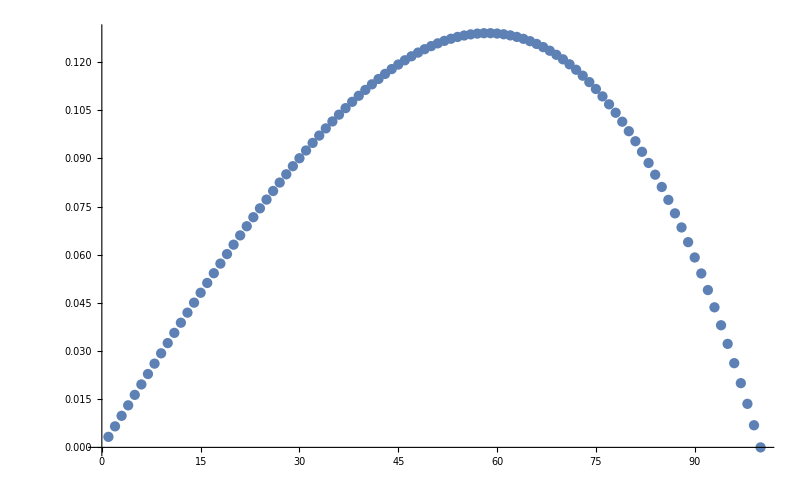

```mathematica
ListPlot[zlk[#,100]&/@Range[1,100]]
```

```mathematica
rp[k_]:=Max[zlk[#,k]&/@Range[1,k]];
```

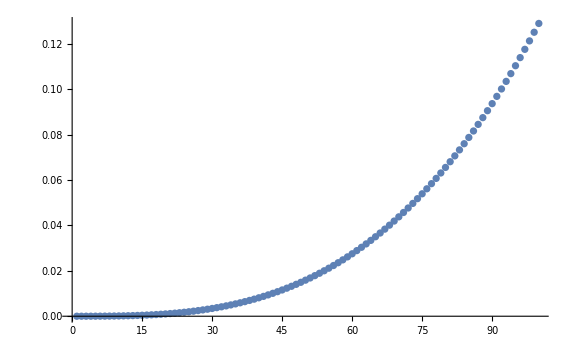

```mathematica
ListPlot[rp/@Range[1,K]]
```

```mathematica
mas = Table[{i,rp[i]},{i,100}];
```

```mathematica
Min[Abs[mas⟦All,2⟧-rd[40,10,600]]]
```

0.0000379526

```mathematica
rdnew[F_,H_,λ_,K_]:=Select[Table[{i,rp[i]},{i,K}],Abs[#⟦2⟧-rd[F,H,λ]]-Min[Abs[mas⟦All,2⟧-rd[F,H,λ]]]==0&]⟦1⟧;
```

```mathematica
rdnew[40,10,600,100]
```

{16,0.000517953}

```mathematica
Xkfor5[rdnew[40,10,600,100]⟦1⟧]
```

0.134632

```mathematica
Manipulate[Grid[{{
Show[
ListPlot[rp/@Range[1,K],AxesLabel->{"K","R"},PlotRange->{{0,102},{-0.01,rp[K]*1.01}},
AxesStyle->Directive[Arrowheads[0.02]],
ImageSize->600],
ListPlot[{point},PlotMarkers->{Automatic, Medium},PlotStyle->Red]
]
},
{
mas=Table[{i,Ykfor4[i]},{i,1,K}];
point=Select[mas,Abs[#⟦2⟧-rd[F,H,λ]]-Min[Abs[mas⟦All,2⟧-rd[F,H,λ]]]==0&]⟦1⟧
}}],
{λ,380,780}
]
```